```mathematica
Limit[Sin[x]/x,x->0]
```

1

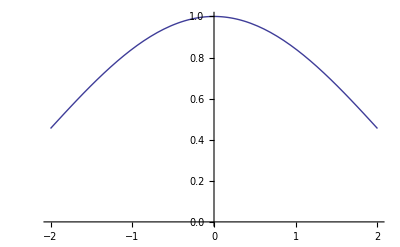

```mathematica
Plot[Sin[x]/x,{x,-2,2},PlotRange->{0,1}]
```

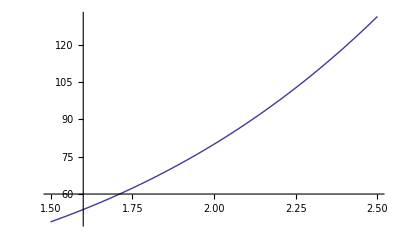

```mathematica
Clear[f];
f[x_]:=(x^5-32)/(x-2);
Plot[f[x],{x,1.5,2.5}]
```

```mathematica
Limit[f[x],x->2]
```

80

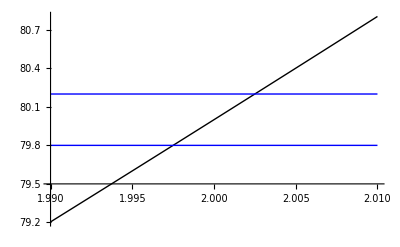

```mathematica
ϵ:=0.2;
y1:=80-ϵ;
y2:=80+ϵ;
Plot[{f[x],y1,y2},{x,1.99,2.01},
PlotStyle->{RGBColor[0,0,0],RGBColor[0,0,1],RGBColor[0,0,1]}]
```

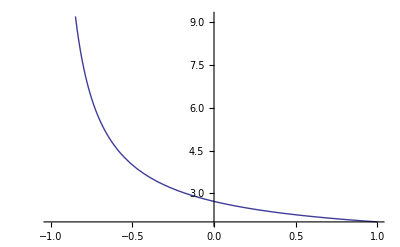

```mathematica
Clear[f];
f[x_]:=(1+x)^(1/x);
Plot[f[x],{x,-1,1}]
```

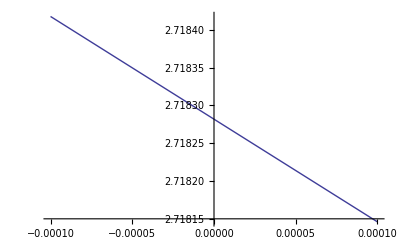

```mathematica
Plot[f[x],{x,-.0001,.0001}]
```

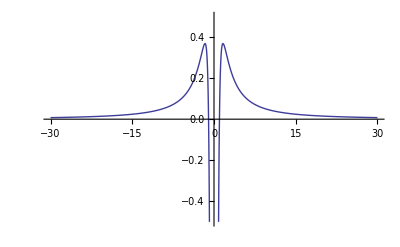

```mathematica
Clear[f];
f[x_]:=Log[x^2]/x^2;
Plot[f[x],{x,-30,30},PlotRange->{-.5,.5}]
```